```mathematica
(*web SU(4)*)
```

```mathematica
a={({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}),({{0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}}),({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}),({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}}),({{0, 0, -ⅈ, 0}, {0, 0, 0, -ⅈ}, {ⅈ, 0, 0, 0}, {0, ⅈ, 0, 0}}),({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}),({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}),({{0, 0, 0, -ⅈ}, {0, 0, -ⅈ, 0}, {0, ⅈ, 0, 0}, {ⅈ, 0, 0, 0}}),({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, -1, 0}}),({{0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}, {0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}}),({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}}),({{0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}, {0, 0, 0, ⅈ}, {0, 0, -ⅈ, 0}}),({{0, 0, 1, 0}, {0, 0, 0, -1}, {1, 0, 0, 0}, {0, -1, 0, 0}}),({{0, 0, -ⅈ, 0}, {0, 0, 0, ⅈ}, {ⅈ, 0, 0, 0}, {0, -ⅈ, 0, 0}}),({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}})};
```

```mathematica
a0=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(*Dodecahedron X15 Lorentz polynomial*)
```

```mathematica
p[z_]=1-131*z^5+131*z^10+ z^15;
```

```mathematica
(*roots*)
```

```mathematica
r[i_]:=z/.NSolve[p[z]==0,z][[i]]
```

```mathematica
w=Table[r[i],{i,15}]
```

{-2.65528,-0.820526-2.52532 ⅈ,-0.820526+2.52532 ⅈ,-0.80655-0.585993 ⅈ,-0.80655+0.585993 ⅈ,-0.305615-0.222042 ⅈ,-0.305615+0.222042 ⅈ,0.116734-0.359272 ⅈ,0.116734+0.359272 ⅈ,0.308075-0.948156 ⅈ,0.308075+0.948156 ⅈ,0.377761,0.99695,2.14816-1.56073 ⅈ,2.14816+1.56073 ⅈ}

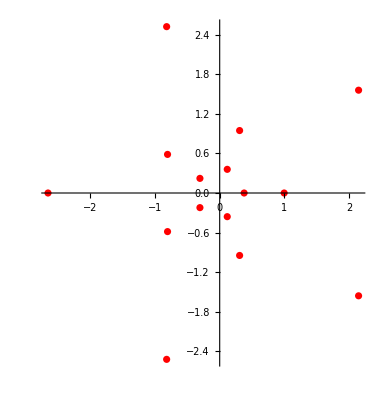

```mathematica
ComplexListPlot[w,PlotStyle->Red]
```

```mathematica
m=a0+Sum[r[i]*a[[i]],{i,15}]
```

{{2.02202+3.86401 ⅈ,-5.06386+0.802037 ⅈ,-0.784339-1.92761 ⅈ,-1.92112-1.15092 ⅈ},{-0.0132241-0.0834937 ⅈ,-0.633253-4.30809 ⅈ,0.591345+1.36154 ⅈ,0.343225+2.36872 ⅈ},{1.16514+0.755622 ⅈ,-0.586425+0.978858 ⅈ,-1.66308+1.18663 ⅈ,-5.29733+0.839015 ⅈ},{0.693739-0.301305 ⅈ,-3.95023-3.54071 ⅈ,-0.246693-1.55756 ⅈ,4.2743-0.742544 ⅈ}}

```mathematica
Dimensions[m]
```

{4,4}

```mathematica
tr=Tr[m]
```

4.+0. ⅈ

```mathematica
dt=Det[m]
```

-126.006+15.8513 ⅈ

```mathematica
Det[m/dt^(1/4)]//Chop
```

1.

```mathematica
(* x4 polynomial on SL(4,C)*)
```

```mathematica
(ArcSin[Sqrt[0.231208]])*(180./Pi)
```

28.7403

```mathematica
(*Weak angle phased*)
```

```mathematica
s0=-ArcSin[Sqrt[0.231208]]
```

-0.501614

```mathematica
msl=ExpandAll[(a0+Sum[z-s0*r[i]*a[[i]],{i,15}])/dt^(1/4)]
```

{{(0.723727+0.112336 ⅈ)+(3.25684-3.05918 ⅈ) z,(-0.469464+0.605392 ⅈ)+(3.25684-3.05918 ⅈ) z,(-0.282621-0.1297 ⅈ)+(3.25684-3.05918 ⅈ) z,(-0.326973+0.0711845 ⅈ)+(3.25684-3.05918 ⅈ) z},{(-0.0099818-0.00774059 ⅈ)+(3.25684-3.05918 ⅈ) z,(-0.401483-0.506062 ⅈ)+(3.25684-3.05918 ⅈ) z,(0.203692+0.0877918 ⅈ)+(3.25684-3.05918 ⅈ) z,(0.279705+0.222869 ⅈ)+(3.25684-3.05918 ⅈ) z},{(0.204199-0.0368998 ⅈ)+(3.25684-3.05918 ⅈ) z,(0.0362703+0.166601 ⅈ)+(3.25684-3.05918 ⅈ) z,(0.0484767+0.197729 ⅈ)+(3.25684-3.05918 ⅈ) z,(-0.491108+0.633304 ⅈ)+(3.25684-3.05918 ⅈ) z},{(0.0447322-0.103786 ⅈ)+(3.25684-3.05918 ⅈ) z,(-0.792446+0.0184905 ⅈ)+(3.25684-3.05918 ⅈ) z,(-0.186208-0.144399 ⅈ)+(3.25684-3.05918 ⅈ) z,(0.497769-0.619784 ⅈ)+(3.25684-3.05918 ⅈ) z}}

```mathematica
TableForm[msl]
```

(0.723727+0.112336 ⅈ)+(3.25684-3.05918 ⅈ) z | (-0.469464+0.605392 ⅈ)+(3.25684-3.05918 ⅈ) z | (-0.282621-0.1297 ⅈ)+(3.25684-3.05918 ⅈ) z | (-0.326973+0.0711845 ⅈ)+(3.25684-3.05918 ⅈ) z
(-0.0099818-0.00774059 ⅈ)+(3.25684-3.05918 ⅈ) z | (-0.401483-0.506062 ⅈ)+(3.25684-3.05918 ⅈ) z | (0.203692+0.0877918 ⅈ)+(3.25684-3.05918 ⅈ) z | (0.279705+0.222869 ⅈ)+(3.25684-3.05918 ⅈ) z
(0.204199-0.0368998 ⅈ)+(3.25684-3.05918 ⅈ) z | (0.0362703+0.166601 ⅈ)+(3.25684-3.05918 ⅈ) z | (0.0484767+0.197729 ⅈ)+(3.25684-3.05918 ⅈ) z | (-0.491108+0.633304 ⅈ)+(3.25684-3.05918 ⅈ) z
(0.0447322-0.103786 ⅈ)+(3.25684-3.05918 ⅈ) z | (-0.792446+0.0184905 ⅈ)+(3.25684-3.05918 ⅈ) z | (-0.186208-0.144399 ⅈ)+(3.25684-3.05918 ⅈ) z | (0.497769-0.619784 ⅈ)+(3.25684-3.05918 ⅈ) z

```mathematica
f[z_]=ExpandAll[CharacteristicPolynomial[msl,z]/(-(12.027353078679127-12.236707767254607 ⅈ))]//Chop
```

(-0.00255937-0.00280453 ⅈ)+(0.0810226+0.106623 ⅈ) z+(0.109839-0.67331 ⅈ) z^2-(1.11423-0.953829 ⅈ) z^3+1. z^4

```mathematica
Det[msl]
```

(0.0651007+0.00241276 ⅈ)-(2.31729+0.314017 ⅈ) z-(7.10543×10^-15+3.55271×10^-15 ⅈ) z^2+(8.32684×10^-15+3.06821×10^-15 ⅈ) z^3

```mathematica
v=z/.NSolve[f[z]==0,z]
```

{0.0314868+0.000996957 ⅈ,0.0332337-0.317031 ⅈ,0.443896-0.0450648 ⅈ,0.605612-0.59273 ⅈ}

```mathematica
max=Max[Norm/@v]+0.25
```

1.0974

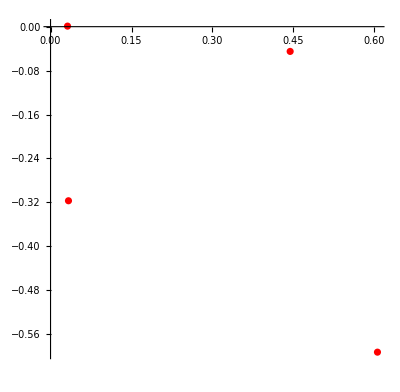

```mathematica
ComplexListPlot[v,PlotStyle->Red]
```

```mathematica
N[(2+Sqrt[2.125])]
```

3.45774

```mathematica
ga=ComplexPlot[f[z],{z,-max-I*max,max+I*max},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
gb=ComplexPlot3D[f[z],{z,-max-I*max,max+I*max},ColorFunction->"CyclicReImLogAbs",ImageSize->2000,PlotPoints->100];
```

```mathematica
g1=JuliaSetPlot[f[x]*12,x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All];
```

```mathematica
g2=ListPlot[JuliaSetPoints[f[x]*12,x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All];
```

```mathematica
Export["Julia_X15doceahedral_SU4_Projection_Polynomial_Phase!Neg28p7_scale12_grid.jpg",GraphicsGrid[{{ga,gb}, 
 {g1,g2}},ImageSize->4000]]
```

Julia_X15doceahedral_SU4_Projection_Polynomial_Phase!Neg28p7_scale12_grid.jpg

```mathematica
gout=ParallelTable[JuliaSetPlot[f[x]*i,x,ColorFunction->Hue,ImageSize->{1080,1080},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False,PlotRange->All],{i,10.,13.,1/200.}];
```

```mathematica
Export["Julia_X15doceahedral_SU4_Projection_Polynomial_Phase!Neg28p7_scaled10to13_200_movie.mp4",gout]
```

```mathematica
(*end*)
```